Dodelson 8.3

### Excercise 8.3. Determine R[η_*] when Ω_b h^2=.01,.02.

```mathematica
<<Dodelson`Definitions`
<<Dodelson`CommonParameters`
RecombinationSubs;
SoundSubs;
EnergyDenSubs;
```

```mathematica
ClearAll[a,tmp,T,R1,R2]

Print["We take the definition  ",defR,"
with the relationships : ",
sT0=Subscript[T, 0]->2.348 10^-4  ,"(eV) temperature now and
",sT2=SubStar[T]-> .2,"(eV) at recombination and 
",s3=SubStar[a] ->Subscript[T, 0]/SubStar[T]," the scale parameter at recombination "
]
```

We take the definition  R(a_):=(3 ρ_m(a))/(4 ρ_γ(a))
with the relationships : T_0→0.0002348(eV) temperature now and
T_*→0.2(eV) at recombination and 
a→T_0/(T_*) the scale parameter at recombination

The speed of sound is define, Eqn.8.19 : c_s(a_):=√(1/(3 (R(a)+1)))

For the values : Ω_m→0.01/h^2 and   Ω_m→0.02/h^2
and we have : R(a)→(3 a h^2 Ω_m)/(4 C_γ)
and c_s(a_):=√(1/(3 (R(a)+1))) => (√(1/((3 a Ω_m h^2)/(4 C_γ)+1)))/(√3) => c_s1[a] == 0.0331327 √(1/(1. a+0.00329333)) for .01 case
and c_s2[a] == 0.0234284 √(1/(1. a+0.00164667)) for .02 case.

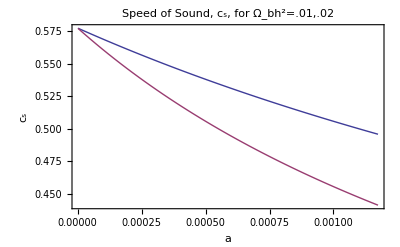

```mathematica
Print["The speed of sound is define, Eqn.8.19 : ",Eqn819
]
ReleaseHold[Eqn819];
ReleaseHold[defR];
ReleaseHold[defRhoG]
ReleaseHold[defRhoM]

Print["For the values : ",
s1=Subscript[Ω, m]->.01/h^2 ," and   ",
s2=Subscript[Ω, m]->.02/h^2,"
and we have : ",
tmp=HoldForm[R[a]]->R[a],"
and ",Eqn819," => ",Subscript[c, s][a]," => c_s1[a] == ",cs1[a_]:=Subscript[c, s][a]/.s1/.Subscript[C, γ]->2.47 10^-5//Simplify;
cs1[a]," for .01 case
and c_s2[a] == ",cs2[a_]:=Subscript[c, s][a]/.s2/.Subscript[C, γ]->2.47 10^-5//Simplify;
cs2[a]," for .02 case."
 ]
a2=SubStar[a]/.s3/.sT0/.sT2;
Plot[{Tooltip[cs1[a],".01"],Tooltip[cs2[a],".02"]},{a,10^-6,a2},PlotLabel->"Speed of Sound, c_s, for Ω_bh^2=.01,.02",Frame->True ,FrameLabel->{a,Subscript[c, s]},LabelStyle->Directive[Bold]]
```